```mathematica
(*position of the bar 1*)
d:=0.15; 
x0:=0;
y0:=d;
z0:=d;

(*constants*)
mx:=1.05*10^6; (*magnetization along x*)
my:=0; (*magnetization along y*)
mz:=0; (*magnetization along z*)
u0:=4π*10^-7 ;
V:=0.750; (*volume*)
n:=0.2; (*range of all plots*)
step:=0.005;
```

```mathematica
(*components of the B field - bar 1*)
```

```mathematica
Bx[x_,y_,z_]:=u0/(4*π*((x-x0)^2+(y-y0)^2+(z-z0)^2)^(3/2))*((3*(mx*(x-x0)+my*(y-y0)+mz*(z-z0))*V*(x-x0))/((x-x0)^2+(y-y0)^2+(z-z0)^2)-mx*V)
```

```mathematica
By[x_,y_,z_]:=u0/(4*π*((x-x0)^2+(y-y0)^2+(z-z0)^2)^(3/2))*((3*(mx*(x-x0)+my*(y-y0)+mz*(z-z0))*V*(y-y0))/((x-x0)^2+(y-y0)^2+(z-z0)^2)-my*V)
```

```mathematica
Bz[x_,y_,z_]:=u0/(4*π*((x-x0)^2+(y-y0)^2+(z-z0)^2)^(3/2))*((3*(mx*(x-x0)+my*(y-y0)+mz*(z-z0))*V*(z-z0))/((x-x0)^2+(y-y0)^2+(z-z0)^2)-mz*V)
```

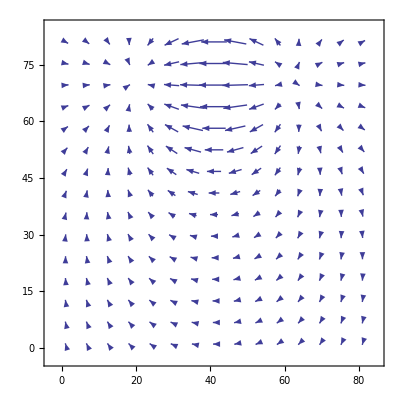

```mathematica
ListVectorPlot[Table[{Bx[x,0,z],Bz[x,0,z]},{x,-n,n,step},{z,-n,n,step}]]
```

```mathematica
(*position of the bar 2*)
x02:=0;
y02:=d;
z02:=-d;
mx2:=-1.05*10^6;
```

```mathematica
(*components of the B field - bar 2*)
```

```mathematica
Bx2[x_,y_,z_]:=u0/(4*π*((x-x02)^2+(y-y02)^2+(z-z02)^2)^(3/2))*((3*(mx2*(x-x02)+my*(y-y02)+mz*(z-z02))*V*(x-x02))/((x-x02)^2+(y-y02)^2+(z-z02)^2)-mx2*V)
```

```mathematica
By2[x_,y_,z_]:=u0/(4*π*((x-x02)^2+(y-y02)^2+(z-z02)^2)^(3/2))*((3*(mx2*(x-x02)+my*(y-y02)+mz*(z-z02))*V*(y-y02))/((x-x02)^2+(y-y02)^2+(z-z02)^2)-my*V)
```

```mathematica
Bz2[x_,y_,z_]:=u0/(4*π*((x-x02)^2+(y-y02)^2+(z-z02)^2)^(3/2))*((3*(mx2*(x-x02)+my*(y-y02)+mz*(z-z02))*V*(z-z02))/((x-x02)^2+(y-y02)^2+(z-z02)^2)-mz*V)
```

```mathematica
(*total contribution of the bar 1 and 2 along direction x and z*)
```

```mathematica
Btotx[x_,y_,z_]:=Bx[x,y,z]+Bx2[x,y,z]
Btotz[x_,y_,z_]:=Bz[x,y,z]+Bz2[x,y,z]
```

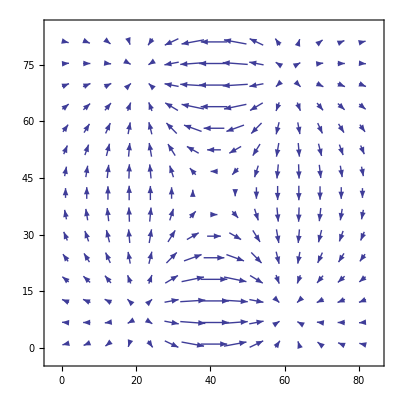

```mathematica
ListVectorPlot[Table[{Btotx[x,0,z],Btotz[x,0,z]},{x,-n,n,step},{z,-n,n,step}]]
```

```mathematica
(*position of the bar 3*)
x03:=0;
y03:=-d;
z03:=-d;
mx3:=-1.05*10^6;
```

```mathematica
(*components of the B field - bar 3*)
```

```mathematica
Bx3[x_,y_,z_]:=u0/(4*π*((x-x03)^2+(y-y03)^2+(z-z03)^2)^(3/2))*((3*(mx3*(x-x03)+my*(y-y03)+mz*(z-z03))*V*(x-x03))/((x-x03)^2+(y-y03)^2+(z-z03)^2)-mx3*V)
By3[x_,y_,z_]:=u0/(4*π*((x-x03)^2+(y-y03)^2+(z-z03)^2)^(3/2))*((3*(mx3*(x-x03)+my*(y-y03)+mz*(z-z03))*V*(y-y03))/((x-x03)^2+(y-y03)^2+(z-z03)^2)-my*V)
```

```mathematica
Bz3[x_,y_,z_]:=u0/(4*π*((x-x03)^2+(y-y03)^2+(z-z03)^2)^(3/2))*((3*(mx3*(x-x02)+my*(y-y02)+mz*(z-z02))*V*(z-z02))/((x-x03)^2+(y-y03)^2+(z-z03)^2)-mz*V)
```

```mathematica
(*total contribution of the bar 1, 2 and 3 along direction x and z*)
```

```mathematica
Btotx2[x_,y_,z_]:=Bx[x,y,z]+Bx2[x,y,z]+Bx3[x,y,z]
Btotz2[x_,y_,z_]:=Bz[x,y,z]+Bz2[x,y,z]+Bz3[x,y,z]
```

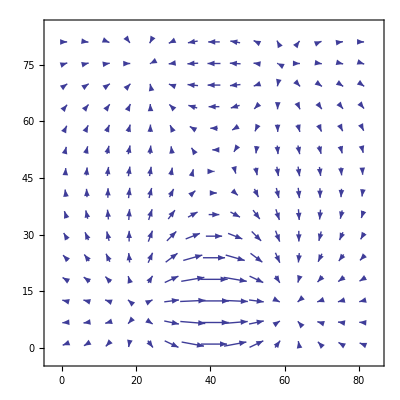

```mathematica
ListVectorPlot[Table[{Btotx2[x,0,z],Btotz2[x,0,z]},{x,-n,n,step},{z,-n,n,step}]]
```

```mathematica
(*position of the bar 4*)
x04:=0;
y04:=-d;
z04:=d;
mx4:=1.05*10^6;
```

```mathematica
(*components of the B field - bar 4*)
```

```mathematica
Bx4[x_,y_,z_]:=u0/(4*π*((x-x04)^2+(y-y04)^2+(z-z04)^2)^(3/2))*((3*(mx4*(x-x04)+my*(y-y04)+mz*(z-z04))*V*(x-x04))/((x-x04)^2+(y-y04)^2+(z-z04)^2)-mx4*V)
By4[x_,y_,z_]:=u0/(4*π*((x-x04)^2+(y-y04)^2+(z-z04)^2)^(3/2))*((3*(mx4*(x-x04)+my*(y-y04)+mz*(z-z04))*V*(y-y04))/((x-x04)^2+(y-y04)^2+(z-z04)^2)-my*V)
```

```mathematica
Bz4[x_,y_,z_]:=u0/(4*π*((x-x04)^2+(y-y04)^2+(z-z04)^2)^(3/2))*((3*(mx4*(x-x04)+my*(y-y04)+mz*(z-z04))*V*(z-z04))/((x-x04)^2+(y-y04)^2+(z-z04)^2)-mz*V)
```

```mathematica
(*total contribution of the bar 1, 2, 3 and 4 along direction x and z*)
```

```mathematica
Btotx3[x_,y_,z_]:=Bx[x,y,z]+Bx2[x,y,z]+Bx3[x,y,z]+Bx4[x,y,z]
Btoty3[x_,y_,z_]:=By[x,y,z]+By2[x,y,z]+By3[x,y,z]+By4[x,y,z]
Btotz3[x_,y_,z_]:=Bz[x,y,z]+Bz2[x,y,z]+Bz3[x,y,z]+Bz4[x,y,z]
```

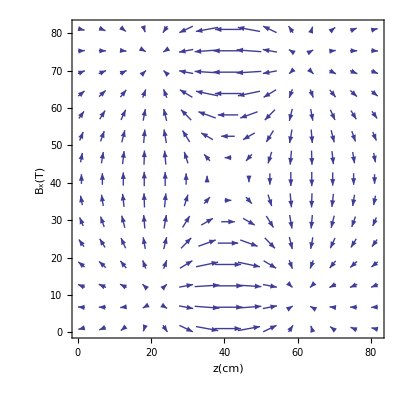

```mathematica
ListVectorPlot[Table[{Btotx3[x,0,z],Btotz3[x,0,z]},{x,-n,n,step},{z,-n,n,step}] ,PlotRange->All,AxesLabel->{"z(cm)","B_x(T)"},AxesStyle->Directive[Black,14],PlotLegends->{"z","x"},ImageSize->400](*field z versus x*)
```

```mathematica
(*this is the final result, except by the fact that the B field is not zero at the center of the quadrupole. Something is translating all the system*)
```

```mathematica
(*now, lets plot the fields*)
```

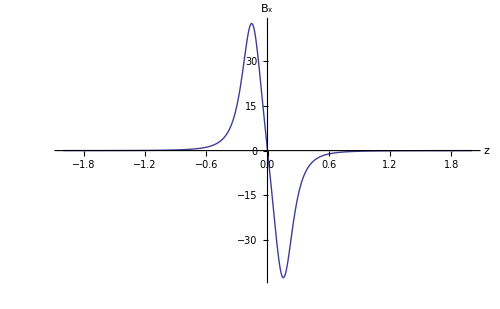

```mathematica
Plot[{Btotx3[0,0,z]},{z,-2,2},PlotRange->All,AxesLabel->{"z","B_x"},AxesStyle->Directive[Black,14],ImageSize->500]
```

```mathematica
Plot[{D[Btotx3[0,0,z],z]},{z,-2,2},PlotRange->All,AxesLabel->{"z","∇_z (B_x)"},AxesStyle->Directive[Black,14],ImageSize->500]
```

General::ivar: -1.99992 is not a valid variable.

General::ivar: -1.91829 is not a valid variable.

General::ivar: -1.83665 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

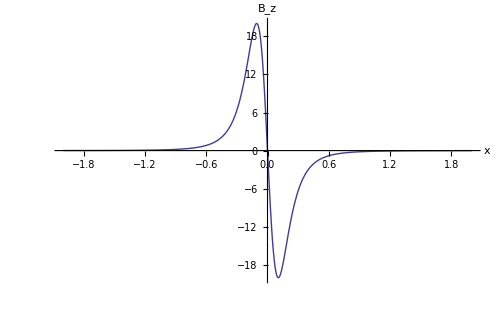

```mathematica
Plot[{Btotz3[x,0,0]},{x,-2,2},PlotRange->All,AxesLabel->{"x","B_z"},AxesStyle->Directive[Black,14],ImageSize->500]
```